```mathematica
μ = Quantity[100,"Kilograms"]
```

100 kg

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[R, e]]
```

```mathematica
Subscript[R, e]= Quantity[6378.1*^3,"Meters"]
```

6.3781×10^6 m

```mathematica
3*Subscript[R, e]
```

1.91343×10^7 m

```mathematica
Symbolize[Subscript[R, 0]]
```

```mathematica
Subscript[R, 0] = 3*Subscript[R, e]
```

1.91343×10^7 m

```mathematica
Symbolize[Subscript[M, e]]
```

```mathematica
Subscript[M, e] = Quantity[5.972*^24 , "Kilograms"]
```

5.972×10^24 kg

```mathematica
G= UnitConvert[Quantity[1,"GravitationalConstant"]]
```

6.674×10^-11 m^3/(kg s^2)

```mathematica
Symbolize[Subscript[l, scale]]
```

```mathematica
Subscript[l, scale] = 1.0
```

1.

```mathematica
l = μ*Subscript[R, 0] * Sqrt[G*Subscript[M, e]/Subscript[R, 0]]*Subscript[l, scale]
```

8.73311×10^12 kg m^2/s

```mathematica
Symbolize[Subscript[v, r,0]]
```

```mathematica
Symbolize[Subscript[v, t,0]]
```

```mathematica
Subscript[v, r,0] = Quantity[500,"Meters"/"Seconds"]
```

500 m/s

```mathematica
Subscript[v, t,0] = Sqrt[G*Subscript[M, e]/Subscript[R, 0]]*Subscript[l, scale]
```

4564.11 m/s

```mathematica
Symbolize[Subscript[E, t]]
```

```mathematica
Subscript[E, t] = (1/2)*μ*(Subscript[v, t,0]^2 + Subscript[v, r,0]^2) - G*Subscript[M, e]*μ/Subscript[R, 0]
```

-1.02906×10^9 kg m^2/s^2

```mathematica
Subscript[E, t] + G*Subscript[M, e]*μ/Subscript[R, 0] - l^2/(2*μ*Subscript[R, 0]^2)
```

1.25×10^7 kg m^2/s^2

```mathematica
r = Quantity["Meters"]
```

1 m

```mathematica
f[r_]:= Subscript[R, 0]*(l/r^2)/Sqrt[2*μ*(Subscript[E, t] + G*Subscript[M, e]*μ/Subscript[R, 0] - l^2/(2*μ*r^2))]
```

```mathematica
f[Subscript[R, 0]]
```

9.12823

```mathematica
Subscript[R, 0]
```

1.91343×10^7 m

```mathematica
g[x_]:= Subscript[R, 0]*(l/Quantity[x,"Meters"]^2)/Sqrt[2*μ*(Subscript[E, t] + G*Subscript[M, e]*μ/Subscript[R, 0] - l^2/(2*μ*Quantity[x,"Meters"]^2))]
```

```mathematica
g[2*^7]
```

2.94345

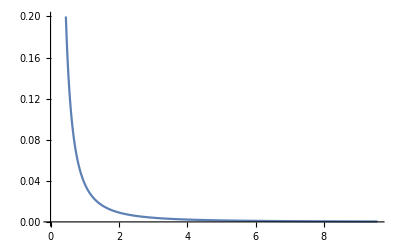

```mathematica
Plot[g[x],{x,2*QuantityMagnitude@Subscript[R, 0],50*QuantityMagnitude@Subscript[R, 0]},PlotRange->{0.0,0.2}]
```

```mathematica
d[x_]:=(-1/Subscript[E, t])*(Subscript[E, t] + G*Subscript[M, e]*μ/Subscript[R, 0] - l^2/(2*μ*Quantity[x,"Meters"]^2))
```

```mathematica
d[1*QuantityMagnitude@Subscript[R, 0]]
```

0.012147

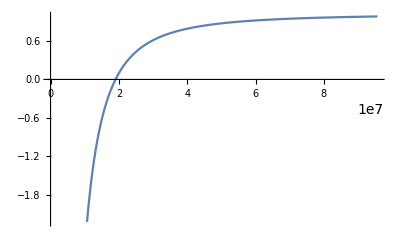

```mathematica
Plot[d[x],{x,0*QuantityMagnitude@Subscript[R, 0],5*QuantityMagnitude@Subscript[R, 0]}]
```